```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\zhangchenhui\custcal

## 函数定义

```mathematica
核算设计=<|"核算设计文本"->Import["custcal.org","Text",CharacterEncoding->"UTF8"]|>;

AssociateTo[核算设计,(* 各表格项内容 *)
RightComposition[
StringCases[
StringExpression[
StartOfLine~~"#+NAME: ",
type:(WordCharacter..)~~":",
(tname:LetterCharacter..)~~Whitespace,
tcnt:Shortest["|-"~~__~~"-|\n"],
"\n"]:>
(tname->
With[{tb=Map[StringTrim@*ToString,
ImportString[
StringReplace[tcnt,{StartOfLine~~"|"~~("+"|"-"|"|"|" ")..~~"|\n"->""}],
"Table","FieldSeparators"->{"|"},"LineSeparators"->{"|\n"}],{2}]},
Switch[type,
"tab",AssociationThread[tb[[2;;,1]]->Map[AssociationThread[Rest@First@tb->#]&,tb[[2;;,2;;]]]],
_,Map[AssociationThread[First[tb]->#]&,Rest[tb]]]])],
Merge[Apply@Join]
]@核算设计["核算设计文本"]];

AssociateTo[核算设计,(* 校验处理 *)
"校验处理"->First[
StringCases[
StringExpression[
StartOfLine~~"#+NAME: 错误处理
#+BEGIN_SRC",
Whitespace,
txt:Longest["<|"~~__~~"|>"]
]:>
ToExpression[txt]]@核算设计["核算设计文本"]]];

AppendTo[核算设计,(* 存储过程名称，来自数据库查询 *)
"存储过程名称"->
<|"110434"->"sp_Cust_QT_Gqzq","140001"->"sp_Cust_CASH_Xjc","140002"->"sp_Cust_CASH_Czc","140004"->"sp_Cust_CASH_Zpc","140008"->"sp_Cust_CASH_Xjlb","140009"->"sp_Cust_CASH_Zplb","140011"->"sp_Cust_CASH_Lxgb","140021"->"sp_Cust_CASH_Xjq","140022"->"sp_Cust_CASH_Czq","140024"->"sp_Cust_CASH_Zpq","140029"->"sp_Cust_CASH_Xjhc","140030"->"sp_Cust_CASH_Zphc","140055"->"sp_Cust_CASH_Hzc","140057"->"sp_Cust_CASH_Hzq","140203"->"sp_Cust_HLHG_Cyks","140205"->"sp_Cust_HLHG_Kslb","140211"->"sp_Cust_CASH_Otcr","140212"->"sp_Cust_CASH_Otcc","150001"->"sp_Cust_ZTG_Zqhc","150002"->"sp_Cust_ZTG_Zqlb","150032"->"sp_Cust_HLHG_Hlrl","160021"->"sp_Cust_SFCG_Yhzq","160022"->"sp_Cust_SFCG_Zqyh","160031"->"sp_Cust_SFCG_Tzc","160032"->"sp_Cust_SFCG_Tzq","168007"->"sp_Cust_SFCG_Tzzr","168008"->"sp_Cust_SFCG_Tzzc","220000"->"sp_Cust_PT_Buy","220006"->"sp_Cust_BJHG_Rqhg","220007"->"sp_Cust_YDGH_Ydhg","220010"->"sp_Cust_HLHG_Hgrz","220012"->"sp_Cust_PG_Pgjk","220030"->"sp_Cust_PG_Psgf","220031"->"sp_Cust_PG_Psjk","220032"->"sp_Cust_QT_Zdjy","220033"->"sp_Cust_QT_Cxzd","220035"->"sp_Cust_BJHG_Rzgh","220038"->"sp_Cust_ETF_Sgzr_Yc","220041"->"sp_Cust_ETF_Xjtd_Yc","220043"->"sp_Cust_YDGH_Rzgh","220049"->"sp_Cust_KFJJ_JJsg","220058"->"sp_Cust_ZZXQ_Xqkk","220059"->"sp_Cust_ZZXQ_Xqzg","220090"->"sp_Cust_KFJJ_Zhsg","220091"->"sp_Cust_KFJJ_Zhsh","220094"->"sp_Cust_GGT_Buy","220095"->"sp_Cust_GGT_Sale","220096"->"sp_Cust_GGT_Hlff","220097"->"sp_Cust_GGT_Zhf","220099"->"sp_Cust_GGT_Qzmc","220100"->"sp_Cust_PT_Tnmr","220118"->"sp_Cust_GGT_Zdjy","220119"->"sp_Cust_GGT_Czjy","220121"->"sp_Cust_GGT_Gong","221001"->"sp_Cust_PT_Sale","221003"->"sp_Cust_BJHG_Rzhg","221004"->"sp_Cust_YDGH_Rzhg","221007"->"sp_Cust_HLHG_Hlrz","221008"->"sp_Cust_ZQ_Zqdx","221009"->"sp_Cust_ZQ_Zqdf","221011"->"sp_Cust_PG_Pgqz","221013"->"sp_Cust_PG_Pgrz","221023"->"sp_Cust_BJHG_Rztq","221033"->"sp_Cust_BJHG_Rqgh","221034"->"sp_Cust_BJHG_Rqtq","221036"->"sp_Cust_ETF_Sgzc","221042"->"sp_Cust_QT_Xsks","221043"->"sp_Cust_YDGH_Rqgh","221049"->"sp_Cust_KFJJ_Jjsh","221101"->"sp_Cust_PT_Tnmc","222003"->"sp_Cust_ZTG_Ztgf","222004"->"sp_Cust_QT_Tpqr","222006"->"sp_Cust_QT_Cxsf","240507"->"sp_Cust_KFJJ_Hlbr","552030"->"sp_Cust_RZRQ_Rqyqs","552016"->"sp_Cust_RZRQ_Rqyqs","940008"->"sp_Cust_SFCG_Xjlb","940029"->"sp_Cust_SFCG_Xjhc","553003"->"sp_Cust_RZRQ_Rqjr","550001"->"sp_Cust_RZRQ_Dbmr","550002"->"sp_Cust_RZRQ_Rzmr","550003"->"sp_Cust_RZRQ_Mqhk","552003"->"sp_Cust_RZRQ_Rqyqs","140032"->"sp_Cust_CASH_Fxgb","140124"->"sp_Cust_CASH_Czpq","140200"->"sp_Cust_GPZY_Lxks","140202"->"sp_Cust_CASH_Zpqr","140502"->"sp_Cust_BRBC_Bxhc","150028"->"sp_Cust_ZTG_Nbzc","150030"->"sp_Cust_HLHG_Gfrl","150031"->"sp_Cust_ZTG_Ncqx","160024"->"sp_Cust_SFCG_Czzy","220003"->"sp_Cust_ZYHG_Rqhg","220004"->"sp_Cust_XG_Xgrz","220005"->"","220015"->"sp_Cust_ZTG_Ztgr","220016"->"sp_Cust_QT_Zdrz","220023"->"sp_Cust_XG_Xgsg","220024"->"sp_Cust_LOF_Rgqr","220027"->"sp_Cust_XG_Sgzq","220034"->"sp_Cust_ZYHG_Rzgh","220039"->"sp_Cust_ETF_Shzr","220040"->"sp_Cust_ETF_XjtdBk","220042"->"sp_Cust_ETF_Xjce","220047"->"sp_Cust_ETF_Sgsf","220048"->"sp_Cust_ETF_Shsf","220056"->"sp_Cust_KFJJ_Cfzg","220057"->"sp_Cust_KFJJ_Hbzg","220060"->"sp_Cust_ZYHG_Zyck","220084"->"sp_Cust_LOF_Szsg","220085"->"sp_Cust_LOF_Szsh","220114"->"sp_Cust_GGT_Sgss","220116"->"sp_Cust_GGT_Fjyc","220135"->"sp_Cust_LOF_LofRG","220136"->"sp_Cust_LOF_Rgfk","220137"->"sp_Cust_KFJJ_Jjsz","220138"->"sp_Cust_KFJJ_Jjxz","221002"->"sp_Cust_ZYHG_Rzhg","221006"->"sp_Cust_ZTG_Dbzc","221012"->"sp_Cust_PG_Tktx","221014"->"sp_Cust_ZTG_Ztgc","221017"->"sp_Cust_ZZZG_Hszc","221019"->"sp_Cust_ZZZG_Hszj","221024"->"sp_Cust_XG_Sghk","221032"->"sp_Cust_QT_Czzc","221035"->"sp_Cust_ZYHG_Rqgh","221037"->"sp_Cust_ETF_Shzc_Yc","221038"->"sp_Cust_ETF_XjtdTk","221039"->"sp_Cust_ETF_XjceFk","221040"->"sp_Cust_ETF_XjtdFk","221056"->"sp_Cust_KFJJ_Hbjg","221057"->"sp_Cust_KFJJ_Cfjg","221060"->"sp_Cust_ZYHG_Zyrk","221204"->"sp_Cust_GPZY_Rz","221207"->"sp_Cust_GPZY_Rq","221243"->"sp_Cust_GPZY_Rzgh","221251"->"sp_Cust_GPZY_Rzbz","221253"->"sp_Cust_GPZY_Rzgh","221343"->"sp_Cust_GPZY_Rqgh","221350"->"sp_Cust_GZYF_Edzc","221351"->"sp_Cust_GZYF_Edzx","240508"->"sp_Cust_KFJJ_Rgbc","240509"->"sp_Cust_KFJJ_Sgbc","240510"->"sp_Cust_KFJJ_Dsde","240511"->"sp_Cust_KFJJ_Shbr","240512"->"sp_Cust_KFJJ_Qsbr","240513"->"sp_Cust_KFJJ_Rgsb","240514"->"sp_Cust_KFJJ_Sgsb","240515"->"sp_Cust_KFJJ_Dssb","240562"->"sp_Cust_BRBC_Ksbr","260508"->"sp_Cust_BRBC_Jrbc","260512"->"sp_Cust_BRBC_Jrqs","553001"->"sp_Cust_RZRQ_Rzjr","553002"->"sp_Cust_RZRQ_Rzjc","550004"->"sp_Cust_RZRQ_Rzpc","550005"->"sp_Cust_RZRQ_Dbmc","550007"->"sp_Cust_RZRQ_Mqhq","551001"->"sp_Cust_ZTG_Dbzc","551004"->"sp_Cust_RZRQ_Rqzy","551005"->"sp_Cust_ZTG_Dbzr","551007"->"sp_Cust_RZRQ_Hqhc","551008"->"sp_Cust_RZRQ_Yqzc","580509"->"sp_Cust_ZZXQ_Tjsd","552037"->"sp_Cust_RZRQ_Rqyqs","551020"->"sp_Cust_RZRQ_Jjcf","551021"->"sp_Cust_RZRQ_Jjcf","552001"->"sp_Cust_RZRQ_Chlx","552006"->"sp_Cust_RZRQ_Yqlx","552008"->"sp_Cust_RZRQ_Rqyqs","552009"->"sp_Cust_RZRQ_Rqyqs","552011"->"sp_Cust_RZRQ_Ylfx","552012"->"sp_Cust_RZRQ_Yzfx","552015"->"sp_Cust_RZRQ_Rqyqs","552017"->"sp_Cust_RZRQ_Chbj","552018"->"sp_Cust_RZRQ_Rqfz","552034"->"sp_Cust_RZRQ_Tcqe","552036"->"sp_Cust_RZRQ_Tckx","554007"->"sp_Cust_RZRQ_Rqzy","550006"->"sp_Cust_RZRQ_Rqmc","550008"->"sp_Cust_RZRQ_Rqpc","140033"->"","140501"->"","160023"->"","220018"->"sp_Cust_ZZZG_Zgzc","220108"->"sp_Cust_GGT_Lgxj","220109"->"sp_Cust_GGT_Gssg","220115"->"sp_Cust_GGT_Fjyr","221031"->"sp_Cust_ZZZG_Zglk","221050"->"","221090"->"sp_Cust_ZRT_Zqcj","221091"->"sp_Cust_ZRT_Ghzq","221092"->"sp_Cust_ZRT_Ghlx","240502"->"","240521"->"","552039"->"","940010"->"sp_Cust_SFCG_Zyzj","940011"->"sp_Cust_SFCG_Zyzj","940012"->"sp_Cust_SFCG_Zyzj","940013"->"sp_Cust_SFCG_Zyzj","141105"->"","141106"->"","220067"->"","220122"->"","220123"->"","221067"->"","221352"->"","221353"->"","221356"->"","221357"->""|>];
```

## 存储过程

### 存储过程管理

```mathematica
Needs["DatabaseLink`"]
conn=OpenSQLConnection[JDBC["Microsoft SQL Server(jTDS)", 
  "10.237.1.10:1433/CustCal"], "Username" -> "sa", "Password" -> "qyb20qyb20","ReadOnly"->True]
```

SQLConnection[…]

#### 数据库查询存储过程名称

```mathematica
Association[(ToString[First[#]]->Last[#])&/@SQLSelect[conn,"digest_ext",{"digestid","spname"}]]
```

#### 数据库删除所有sp_Cust存储过程

```mathematica
Scan[SQLExecute[conn,#]&,
"drop proc "<>#&/@ Flatten@SQLExecute[conn,"select name from sysobjects where type='P' and name like 'sp_Cust%'"]]
```

#### 数据库更新sp_Cust存储过程

```mathematica
Map[Scan[SQLExecute[conn,#]&,StringSplit[Import["sp\\sp_Cust_BJHG_Rqgh.sql","Text",CharacterEncoding->"Unicode"],{"go","GO"}]]
```

```mathematica
Scan[SQLExecute[conn,#]&,
Query[Flatten,StringSplit[Import[#,"Text",CharacterEncoding->"Unicode"],{"go","GO"}]&]@FileNames["*.sql",FileNameJoin[{$UserDocumentsDirectory,"work","CustCal","dev","sp"}]]]
```

```mathematica
CloseSQLConnection[conn]
```

{}

### 本地生成存储过程

```mathematica
Query[
"核算办法",
Select[#产生方式=="模板"∧#进度=="完成"&],
Export[FileNameJoin[{(*$UserDocumentsDirectory,"work","CustCal","dev",*)"sp",核算设计["存储过程名称"][#业务摘要]<>".sql"}],
TemplateApply[
Import[FileNameJoin[{"templates",#核算类型<>".template"}],"Text",CharacterEncoding->"UTF8"],
Join[
Query["核算对象",All,"数据库对象"]@核算设计,
#,
<|"存储过程"->核算设计["存储过程名称"][#业务摘要],"流通类型"->If[StringLength[#流通类型]==1,"0"<>#流通类型,#流通类型],"转出类型"->If[StringLength[#转出类型]==1,"0"<>#转出类型,#转出类型],
"校验处理"->StringRiffle[TemplateApply["    if (`错误条件`)
       begin
          select @msg='`错误信息`'
          raiserror(' %s', 12, 1, @msg) with SETERROR
       end",#]&/@核算设计["校验处理",#校验],"\n\n"]|>
]],"Text",CharacterEncoding->"Unicode"]&]@核算设计//Column
```

sp\sp_Cust_PT_Buy.sql
sp\sp_Cust_PT_Tnmr.sql
sp\sp_Cust_GGT_Buy.sql
sp\sp_Cust_KFJJ_JJsg.sql
sp\sp_Cust_KFJJ_Zhsg.sql
sp\sp_Cust_RZRQ_Dbmr.sql
sp\sp_Cust_XG_Xgsg.sql
sp\sp_Cust_XG_Sghk.sql
sp\sp_Cust_XG_Sgzq.sql
sp\sp_Cust_XG_Xgrz.sql
sp\sp_Cust_PG_Pgqz.sql
sp\sp_Cust_PG_Pgjk.sql
sp\sp_Cust_PG_Pgrz.sql
sp\sp_Cust_PG_Psjk.sql
sp\sp_Cust_PG_Psgf.sql
sp\sp_Cust_GGT_Sgss.sql
sp\sp_Cust_GGT_Fjyc.sql
sp\sp_Cust_GGT_Gong.sql
sp\sp_Cust_PT_Sale.sql
sp\sp_Cust_PT_Tnmc.sql
sp\sp_Cust_GGT_Sale.sql
sp\sp_Cust_GGT_Qzmc.sql
sp\sp_Cust_KFJJ_Jjsh.sql
sp\sp_Cust_KFJJ_Zhsh.sql
sp\sp_Cust_ZYHG_Rzhg.sql
sp\sp_Cust_YDGH_Rzhg.sql
sp\sp_Cust_ZYHG_Rzgh.sql
sp\sp_Cust_YDGH_Rzgh.sql
sp\sp_Cust_ZYHG_Rqhg.sql
sp\sp_Cust_BJHG_Rqhg.sql
sp\sp_Cust_ZYHG_Rqgh.sql
sp\sp_Cust_BJHG_Rqgh.sql
sp\sp_Cust_BJHG_Rqtq.sql
sp\sp_Cust_ZYHG_Zyck.sql
sp\sp_Cust_ZYHG_Zyrk.sql
sp\sp_Cust_QT_Zdrz.sql
sp\sp_Cust_ZTG_Ztgr.sql
sp\sp_Cust_QT_Czzc.sql
sp\sp_Cust_ZTG_Ztgc.sql
sp\sp_Cust_GGT_Czjy.sql
sp\sp_Cust_HLHG_Hlrz.sql
sp\sp_Cust_GGT_Hlff.sql
sp\sp_Cust_HLHG_Hlrl.sql
sp\sp_Cust_ZQ_Zqdx.sql
sp\sp_Cust_HLHG_Hgrz.sql
sp\sp_Cust_CASH_Lxgb.sql
sp\sp_Cust_CASH_Fxgb.sql
sp\sp_Cust_ZQ_Zqdf.sql
sp\sp_Cust_QT_Cxsf.sql
sp\sp_Cust_GGT_Zhf.sql
sp\sp_Cust_ZTG_Ztgf.sql
sp\sp_Cust_ZZXQ_Tjsd.sql
sp\sp_Cust_QT_Xsks.sql
sp\sp_Cust_HLHG_Cyks.sql
sp\sp_Cust_HLHG_Kslb.sql
sp\sp_Cust_YDGH_Ydhg.sql
sp\sp_Cust_YDGH_Rqgh.sql
sp\sp_Cust_BJHG_Rztq.sql
sp\sp_Cust_BJHG_Rzhg.sql
sp\sp_Cust_BJHG_Rzgh.sql
sp\sp_Cust_QT_Zdjy.sql
sp\sp_Cust_QT_Cxzd.sql
sp\sp_Cust_GGT_Zdjy.sql
sp\sp_Cust_QT_Tpqr.sql
sp\sp_Cust_GZYF_Edzc.sql
sp\sp_Cust_GZYF_Edzx.sql
sp\sp_Cust_KFJJ_Hbzg.sql
sp\sp_Cust_KFJJ_Cfjg.sql
sp\sp_Cust_SFCG_Xjlb.sql
sp\sp_Cust_SFCG_Xjhc.sql
sp\sp_Cust_CASH_Xjlb.sql
sp\sp_Cust_CASH_Xjhc.sql
sp\sp_Cust_CASH_Zplb.sql
sp\sp_Cust_CASH_Zphc.sql
sp\sp_Cust_KFJJ_Cfzg.sql
sp\sp_Cust_KFJJ_Hbjg.sql
sp\sp_Cust_KFJJ_Jjsz.sql
sp\sp_Cust_HLHG_Gfrl.sql
sp\sp_Cust_ZTG_Zqlb.sql
sp\sp_Cust_KFJJ_Jjxz.sql
sp\sp_Cust_QT_Gqzq.sql
sp\sp_Cust_ZTG_Zqhc.sql
sp\sp_Cust_SFCG_Yhzq.sql
sp\sp_Cust_CASH_Czc.sql
sp\sp_Cust_CASH_Xjc.sql
sp\sp_Cust_SFCG_Tzc.sql
sp\sp_Cust_CASH_Zpc.sql
sp\sp_Cust_CASH_Otcr.sql
sp\sp_Cust_SFCG_Tzzr.sql
sp\sp_Cust_CASH_Hzc.sql
sp\sp_Cust_CASH_Zpqr.sql
sp\sp_Cust_SFCG_Zqyh.sql
sp\sp_Cust_SFCG_Czzy.sql
sp\sp_Cust_CASH_Czq.sql
sp\sp_Cust_CASH_Xjq.sql
sp\sp_Cust_CASH_Zpq.sql
sp\sp_Cust_CASH_Otcc.sql
sp\sp_Cust_SFCG_Tzzc.sql
sp\sp_Cust_SFCG_Tzq.sql
sp\sp_Cust_CASH_Hzq.sql
sp\sp_Cust_CASH_Czpq.sql

```mathematica
核算设计["校验处理"]//Dataset
```

### 文本格式化

#### 检查update和insert对应关系

```mathematica
#->TableForm@Select[StringCases[Import[#,"Text",CharacterEncoding->"UTF8"],
"update "~~tbl:("`"~~LetterCharacter..~~"`")~~Whitespace~~
"set "~~(set__/;StringFreeQ[set,"where"])~~Whitespace~~
"where "~~(where__/;StringFreeQ[where,"update"])~~
"insert "~~tbl__~~WhitespaceCharacter...~~Shortest["("~~__~~")"]~~Whitespace~~
"select "~~Shortest[sel__]~~"end"
:>{Sort@Flatten@StringCases[StringTrim@StringSplit[set,","],
{f__~~"="~~f__~~"+"~~v__:>f<>"="<>v,f__~~"="~~f__~~"-"~~v__:>f<>"=-"<>v}],Sort@Select[StringTrim@StringSplit[sel,","],StringFreeQ[{"=0","=''","serverid","orgid","custid","fundid","market","stkcode","ltlx","moneytype","bankcode"}]]}],
First[#]≠Last[#]&]&/@
FileNames["*.template",FileNameJoin[{(*$UserDocumentsDirectory,"work","CustCal","dev","sp"*)"templates"}]]//Column
```

templates\供股缴款.template→{}
templates\债券兑付.template→{}
templates\其它费用.template→{}
templates\利息扣税.template→{}
templates\基金合并.template→{}
templates\基金拆分.template→{}
templates\持仓上账.template→{}
templates\持仓下账.template→{}
templates\新股申购.template→{}
templates\无需核算.template→{}
templates\正股入账.template→{}
templates\申购中签.template→{}
templates\申购还款.template→{}
templates\红利入账.template→{}
templates\红股入账.template→{}
templates\综合费用.template→{}
templates\融券回购.template→{}
templates\融券购回.template→{}
templates\融资回购.template→{}
templates\融资购回.template→{}
templates\行权扣款.template→{}
templates\证券买入.template→{}
templates\证券卖出.template→{}
templates\证券转入.template→{}
templates\证券转出.template→{}
templates\质押入库.template→{}
templates\质押出库.template→{}
templates\资金取出.template→{}
templates\资金存入.template→{}
templates\资金结息.template→{}
templates\资金调整.template→{}
templates\送股上市.template→{}
templates\配股缴款.template→{}
templates\非交易出.template→{}
templates\主模板.template→{}

#### 转化insert语法

```mathematica
txt="                insert `持仓核算`
                 (serverid, orgid, custid, fundid, market, stkcode, ltlx, 
                 stkbuyqty, stkbuyamt, stksaleqty, stksaleamt, stkbuyqty_ex, stkbuyamt_ex, stksaleqty_ex, stksaleamt_ex, 
                 stkztgrqty, stkztgramt, stkztgcqty, stkztgcamt, stkhgqty, stkhlamt, stkpgqty, stkpgamt, 
                 stkqty, stkqty_ch, stkqty_tz, stkqty_tzje, stkpledge, stkdebt, stkdebt_ch, stkloan,
                 stkloan_ch, stkadjust, stkadjust_ch, stkprice, bondintr, mktvalue, aiamount, stkcost,
                 stkcost_ch, aicost, aicost_ch, syvalue, syvalue_ch, lxsr, lxsr_ch, gyvalue,
                 gyvalue_ch, lxjt, lxjt_ch, cjsr, cjsr_ch, jrzc, jrzc_ch, sxf,
                 sxf_ch, jsxf, jsxf_ch, yhs, yhs_ch, lxs, lxs_ch, ghf,
                 ghf_ch, qtfee, qtfee_ch, jtdate, gydate, remark, stkpledge_ch, yearqty,
                 yeargyvalue, yearlxjt)
          values (@serverid, @orgid, @custid, @fundid, @market, @stkcode, '`流通类型`',
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,@stkeffect,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,'',0,0,
                 0,0);";
ass=AssociationThread@@StringCases[txt,{"`持仓核算`"~~Whitespace~~"("~~(k:Except[")"]..)~~")":>StringSplit[StringDelete[k,Whitespace],","],"values"~~Whitespace~~"("~~Longest[v__]~~")":>StringSplit[StringDelete[v,Whitespace],","]}];
TemplateApply[
"          insert <* \"`持仓核算`\" *>
                   (<* StringRiffle[Keys[ass],\", \"] *>)
            select <* StringRiffle[KeyValueMap[#1<>\"=\"<>#2&, ass],\", \"] *>"]
```

```mathematica
txt="      insert `资金核算`
                 (serverid, orgid, custid, fundid, moneytype, bankcode,
                 fundbal, fundbal_ch, fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch,
                 funddebt, funddebt_ch, funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundintr, fundintr_ch,
                 fundaward, fundaward_ch, fundadjust, fundadjust_ch, fundlastbal, totalvalue, tjdate, remark,
                 nav, mktvalue, totalfe, rzlx, rzlx_ch)
          values (@serverid, @orgid, @custid, @fundid, @moneytype, @bankcode,
                 @fundeffect, @fundeffect,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,0,
                 0,0,0,0,0,0,0,'',
                 0,0,0,0,0);";
ass=AssociationThread@@StringCases[txt,{"`资金核算`"~~Whitespace~~"("~~(k:Except[")"]..)~~")":>StringSplit[StringDelete[k,Whitespace],","],"values"~~Whitespace~~"("~~Longest[v__]~~")":>StringSplit[StringDelete[v,Whitespace],","]}];
TemplateApply[
"          insert <* \"`资金核算`\" *>
                  (<* StringRiffle[Keys[ass],\", \"] *>)
            select <* StringRiffle[KeyValueMap[#1<>\"=\"<>#2&, ass],\", \"] *>"]
```

```mathematica
txt1="serverid, orgid, custid, fundid, moneytype, fundlastbal, fundbal, fundbal_ch, 
                     fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch, funddebt, funddebt_ch, 
                     funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundadjust, fundadjust_ch, fundintr, fundintr_ch, 
                     fundaward, fundaward_ch, rzlx, rzlx_ch, bankcode, mktvalue, totalvalue, totalfe, nav, tjdate, remark";
txt2="serverid,orgid,custid,fundid,moneytype,bankcode,fundbal,fundbal_ch,fundsave,fundsave_ch,fundunsave,fundunsave_ch,fundloan,fundloan_ch,funddebt,funddebt_ch,funduncome,funduncome_ch,fundunpay,fundunpay_ch,fundintr,fundintr_ch,fundaward,fundaward_ch,fundadjust,fundadjust_ch,fundlastbal,totalvalue,tjdate,remark,nav,mktvalue,totalfe,rzlx,rzlx_ch";
```

```mathematica
StringSplit[txt1,WhitespaceCharacter...~~","~~WhitespaceCharacter...]~Complement~
StringSplit[txt2,WhitespaceCharacter...~~","~~WhitespaceCharacter...]
```

{}

## 业务流程总结

### 新股业务

新股申购：使用权证代码

## 草稿

```mathematica
(*squre josephus*)NestWhile[a↦Delete[a,List/@(Range[Floor@Sqrt@Length[a]]^2)],Range[#],Length[#]>1&]&/@Range[20]//Flatten
```

{1,2,3,3,5,5,7,7,7,10,10,10,13,13,13,13,17,17,17,17}

```mathematica
(a↦a^2-a+1)/@Floor@Sqrt@Range[20]
```

{1,1,1,3,3,3,3,3,7,7,7,7,7,7,7,13,13,13,13,13}

```mathematica
Position[]
```

```mathematica
s1="serverid, orgid, custid, fundid, moneytype, bankcode,
              fundbal, fundbal_ch, fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch,
              funddebt, funddebt_ch, funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundintr, fundintr_ch,
              fundaward, fundaward_ch, fundadjust, fundadjust_ch, fundlastbal, totalvalue, tjdate, remark,
              nav, mktvalue, totalfe";
s2="serverid, orgid, custid, fundid, moneytype, fundlastbal, fundbal, fundbal_ch, 
                             fundsave, fundsave_ch, fundunsave, fundunsave_ch, fundloan, fundloan_ch, funddebt, funddebt_ch, 
                             funduncome, funduncome_ch, fundunpay, fundunpay_ch, fundadjust, fundadjust_ch, fundintr, fundintr_ch, 
                             fundaward, fundaward_ch, bankcode, mktvalue, totalvalue, totalfe, nav, tjdate, remark";
```

```mathematica
Sort@StringSplit[s1,WhitespaceCharacter...~~","~~Whitespace]==
Sort@StringSplit[s2,WhitespaceCharacter...~~","~~Whitespace]
```

True

```mathematica
Total[(Length@*Permutations)/@IntegerPartitions[#,All,Range[3,#]]]&/@Range[15]
```

{0,0,1,1,1,2,3,4,6,9,13,19,28,41,60}

```mathematica
Total[(Length@*Permutations)/@IntegerPartitions[#,All,Range[3,#]]]&/@Range[15]//FindLinearRecurrence
```

{1,0,1}

```mathematica
IntegerPartitions[15,All,Range[3,15]]
```

{{15},{12,3},{11,4},{10,5},{9,6},{9,3,3},{8,7},{8,4,3},{7,5,3},{7,4,4},{6,6,3},{6,5,4},{6,3,3,3},{5,5,5},{5,4,3,3},{4,4,4,3},{3,3,3,3,3}}

```mathematica
Permutations[{10,1,1}]
```

{{10,1,1},{1,10,1},{1,1,10}}

```mathematica
StringExpression[
StartOfLine~~"#+NAME: 错误处理 
#+BEGIN_SRC",
Whitespace,
txt:Longest["<|"~~__~~"|>"]
]
```

StartOfLine~~#+NAME: 错误处理 
#+BEGIN_SRC~~Whitespace~~txt:Longest[<|~~__~~|>]

```mathematica
FindClique[RelationGraph[DigitCount[BitAnd[#1,#2],2,1]<2&,FromDigits[Reverse@ReplacePart[ConstantArray[0,12],List/@#->1],2]&/@Subsets[Range[12],{4}]]]
```

{{15,113,897,1170,2338,2580,1348,1576,2248}}

```mathematica
Length@First[FindClique[RelationGraph[Length[Intersection[#1,#2]]<2&,Subsets[Range[#],{4}]]]]&/@{4,5,6,7,8,9,10,11}
```

{1,1,1,2,2,3,5,6}

```mathematica
DeleteDuplicatesBy[Subsets[Range[12],{4}]]
```

```mathematica
games=Fold[{bag,game}↦If[AllTrue[bag,Length[Intersection[#,game]]<2&],Append[bag,game],bag],{},Subsets[Range[12],{4}]]
```

{{1,2,3,4},{1,5,6,7},{1,8,9,10},{2,5,8,11},{2,6,9,12},{3,5,10,12},{3,7,9,11},{4,6,10,11},{4,7,8,12}}

```mathematica
games=Fold[{bag,game}↦If[AllTrue[bag,Length[Intersection[#,game]]<2&],Append[bag,game],bag],Partition[Range[16],4],Subsets[Range[16],{4}]]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16},{1,5,9,13},{1,6,10,14},{1,7,11,15},{1,8,12,16},{2,5,10,15},{2,6,9,16},{2,7,12,13},{2,8,11,14},{3,5,11,16},{3,6,12,15},{3,7,9,14},{3,8,10,13},{4,5,12,14},{4,6,11,13},{4,7,10,16},{4,8,9,15}}

```mathematica
RelationGraph[Length[Intersection[#1,#2]]==1&,games]
```

```mathematica
VertexDegree[%]
```

{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

```mathematica
Select[Table[k,{k,Ceiling[10^5/667],Floor[10^6/667]}],Sort[IntegerDigits[667#]]==Range[0,5]&]
```

{456,645}

```mathematica
456*667
```

304152

```mathematica
{Ceiling[10^5/667],Floor[10^6/667]}
```

{150,1499}

```mathematica
FactorInteger[667]
```

{{23,1},{29,1}}

```mathematica
{{0,-1},{1,0}}.{1,1}
```

{-1,1}

```mathematica
Subsets[Tuples[Range[4],2],{2}]
```

{{1,1},{1,2}}

```mathematica
RotationTransform[# Pi/2,Mean[{{1,1},{4,4}}]][{{1,1},{1,2}}]&/@Range[4]
```

{{{4,1},{3,1}},{{4,4},{4,3}},{{1,4},{2,4}},{{1,1},{1,2}}}

```mathematica
Table[Subscript[A, i,j],{i,3},{j,3}]//MatrixForm
```

(A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

```mathematica
Select[SparseArray[Thread[#->1],6]&/@Subsets[Range[6],2],1≤Total@Flatten[#]≤2&]
```

```mathematica
And@@(And@@Thread[#<{1,2,3}]&/@{{a1,a2,a3},{a4,a5,a6},{a7,a8,a9}})
```

a1<1&&a2<2&&a3<3&&a4<1&&a5<2&&a6<3&&a7<1&&a8<2&&a9<3

```mathematica
Point[{{1,1,1},{1,1,2},{1,1,3}}
```

```mathematica
AllTrue[{{1,1,1},{1,1,2},{3,3,3}},RegionMember[Cuboid[{1,1,1},{2,3,4}]]]
```

False

```mathematica
Join@@((SortBy[Total]@Union[Flatten[Permutations/@IntegerPartitions[#,{4},{1,2,3}],1],SameTest->(#1==Reverse[#2]&)]&)/@Range[4,12])
```

{{1,1,1,1},{1,1,1,2},{1,1,2,1},{1,1,1,3},{1,1,2,2},{1,1,3,1},{1,2,1,2},{1,2,2,1},{2,1,1,2},{1,1,2,3},{1,1,3,2},{1,2,1,3},{1,2,2,2},{1,2,3,1},{1,3,1,2},{2,1,1,3},{2,1,2,2},{1,1,3,3},{1,2,2,3},{1,2,3,2},{1,3,1,3},{1,3,2,2},{1,3,3,1},{2,1,2,3},{2,1,3,2},{2,2,1,3},{2,2,2,2},{3,1,1,3},{1,2,3,3},{1,3,2,3},{1,3,3,2},{2,1,3,3},{2,2,2,3},{2,2,3,2},{2,3,1,3},{3,1,2,3},{1,3,3,3},{2,2,3,3},{2,3,2,3},{2,3,3,2},{3,1,3,3},{3,2,2,3},{2,3,3,3},{3,2,3,3},{3,3,3,3}}

```mathematica
IntegerPartitions[#,{3}]&/@{3,4,5}
```

{{1,1,1},{2,1,1},{3,1,1},{2,2,1}}

```mathematica
Join@@(Permutations/@IntegerPartitions[#,{3}]&/@{3,4,5})
```

{{4,1,1},{1,4,1},{1,1,4},{3,2,1},{3,1,2},{2,3,1},{2,1,3},{1,3,2},{1,2,3},{2,2,2}}

```mathematica
Permutations[{3,1,1}]
```

{{3,1,1},{1,3,1},{1,1,3}}

```mathematica
Select[Subsets[Tuples[Range/@{10,10}],{3}],MatrixRank[Differences[#]]==1&];//Timing
```

{0.780005,Null}

```mathematica
Range/@{2,3,4}
```

{{1,2},{1,2,3},{1,2,3,4}}

```mathematica
SparseArray
```

```mathematica
findNCL[n_]:=With[{lines=Select[Subsets[Range[0,26],{3}],MatrixRank[Differences@IntegerDigits[#,3,3]]==1&]},
SelectFirst[Subsets[Range[0,26],{n}],s↦AllTrue[lines,ln↦!ContainsAll[s,ln]]]]
```

```mathematica
ParallelMap[findNCL,{16,17,18}]
```

{{0,1,3,5,7,8,9,11,15,17,19,20,21,23,24,25},Missing[NotFound],Missing[NotFound]}

```mathematica
NCL=IntegerDigits[First[%],3,3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,2},{0,2,1},{0,2,2},{1,0,0},{1,0,2},{1,2,0},{1,2,2},{2,0,1},{2,0,2},{2,1,0},{2,1,2},{2,2,0},{2,2,1}}

```mathematica
Graphics3D[{Ball[NCL,0.1], Opacity[0.1],Cuboid[{0,0,0},{2,2,2}]},Boxed->False]
```

```mathematica
Binomial[16,2] 11
```

1320

```mathematica
Binomial[16,3]
```

560

```mathematica
Differences@IntegerDigits[{21,24,25},3,3]
```

{{0,1,0},{0,0,1}}

```mathematica
Equal@@Subtract@@IntegerDigits[Differences[{21,24,25}],3,3]
```

False

```mathematica
Divide
```

```mathematica
Unequal@@({1,2,3}/{3,6,8})
```

False

```mathematica
Unequal[2,3,3]
```

False

```mathematica
Table[Binomial[k,i],{i,1,5},{k,1,5}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5
0 | 1 | 3 | 6 | 10
0 | 0 | 1 | 4 | 10
0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 1)

```mathematica
m[n_]:=ReplacePart[{i_,j_}/;EvenQ[i]&&j==i/2:>-1]@Table[Binomial[k,i],{i,n},{k,n}]
```

```mathematica
m[4]//MatrixRank
```

4

```mathematica
Table[Binomial[k,i],{i,1,5},{k,1,5}].{-2,1,0,0,0}
```

{0,1,0,0,0}

```mathematica
NullSpace[m[5]]
```

{{-2,1,0,0,0}}

```mathematica
m[5].{-2,1,0,0,0}
```

{0,0,0,0,0}

```mathematica
m[6]//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0 | 0 | 3 | 6 | 10 | 15
0 | 0 | 0 | 1 | 4 | 10 | 20
0 | 0 | 0 | 0 | 0 | 5 | 15
0 | 0 | 0 | 0 | 0 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LinearSolve[Table[Binomial[k,i],{i,0,5},{k,0,5}],{a0,0,a2,0,a4,a5}]
```

{a0+a2+a4-a5,-2 a2-4 a4+5 a5,a2+6 a4-10 a5,-2 (2 a4-5 a5),a4-5 a5,a5}

```mathematica
Sum[Binomial[k,i] x^i]
```

```mathematica
CoefficientList[Sum[2 Subscript[a, i] x(1+x)^i,{i,20}],x]//List
```

```mathematica
FindInstance[{111101111m==(10^n-1)/9,m>0,n>0},{m,n},Integers]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[{111101111 m==1/9 (-1+10^n),m>0,n>0},{m,n},Integers]

```mathematica
Clear[f]
f[n_]:=
Cases[Permutations[Range[n]],p_/;AllTrue[p[[#]]&/@Flatten[Table[i;;j,{i,n-2},{j,i+2,n}],1],!MemberQ[#,(First[#]+Last[#])/2]&]]
```

```mathematica
(f/*Length)/@Range[9]
```

{1,2,4,10,20,48,104,282,496}

```mathematica
t=RandomInteger[{0,1},10]
```

{1,1,0,1,1,1,1,0,0,0}

```mathematica
t[[{{1;;3},3,2}]]
```

Part::pkspec1: The expression {{1;;3},3,2} cannot be used as a part specification.

{1,1,0,1,1,1,1,0,0,0}⟦{{1;;3},3,2}⟧

```mathematica
∀
```

```mathematica
Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}]
```

Extract::psl1: Position specification {{1;;3}} in Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}] is not applicable.

Extract[{1,1,0,1,1,1,1,0,0,0},{{1;;3}}]

```mathematica
f[n_]:=Count[Tuples[{0,1},n],p_/;AllTrue[p[[#]]&/@Flatten[Table[i;;j,{i,n-2},{j,i+2,n}],1],Abs[2Total[#]-Length[#]]<=2&]]
```

```mathematica
Array[f,14]
```

{2,4,6,10,14,22,30,46,62,94,126,190,254,382}

```mathematica
FindGeneratingFunction[{2,4,6,10,14,22,30,46,62,94,126,190,254,382},x]//Factor
```

-(2 (-1-x+x^2))/((-1+x) (-1+2 x^2))

```mathematica
FindSequenceFunction[{2,4,6,10,14,22,30,46,62,94},n]//FullSimplify
```

1/2 (-4+2^(n/2) (3+2 √2+(-1)^(1+n) (-3+2 √2)))

```mathematica
Export["test.gif",Table[Plot[x^t,{x,0,1}],{t,0,10}],"DisplayDurations"->1,"AnimationRepetitions"->2]
```

test.gif

```mathematica
CountsBy[Tuples[{0,1},10],t↦AllTrue[t[[#]]&/@Flatten[Table[i;;j,{i,8},{j,i+2,10}],1],Abs[2Total[#]-Length[#]]<3&]]
```

<|False→930,True→94|>

```mathematica
AllTrue[t[[#]]&/@Flatten[Table[i;;j,{i,8},{j,i+2,10}],1],Total[#]<3&]
```

False

```mathematica
Abs[Subtract@@BinCounts[{1,0,1,1,0},{0,2}]]
```

1

```mathematica
Subscript[A, k_]:=ReIm@Exp[Mod[(k-31),60]/60 2π I]
```

```mathematica
RegionIntersection[Line[{Subscript[A, 6],Subscript[A, 32]}],Line[{Subscript[A, 22],Subscript[A, 38]}]]//FullSimplify
```

Point[{{Root[1-7 #1^2+14 #1^4-8 #1^6+#1^8&,6],0}}]

```mathematica
DateDifference["Jan 2, 2013","Jan 9, 2013","Week"]
```

1 wk

```mathematica
Cashflow@Annuity[{1,p},2]
```

Cashflow[{{1,1+p},{2,1}}]

```mathematica
TimeValue[%,r]//Apart
```

1/(1+r)^2+(1+p)/(1+r)

```mathematica
StringRiffle[Flatten[Table[TemplateApply[
"create index idx_logasset_`node`_2016_`month`
on logasset_`node`_2016_`month`(bizdate,sno,digestid)",
<|"node"->node,"month"->month|>],
{node,{"jd1", "jd2","jd3","bg","rzrq"}},
{month,{"01","02","03","04","05","06","07","08","09","10"}}]],"\n"]
```

```mathematica
(i↦IntegerDigits[i,10,2])/* f/@Range[10]//InputForm
```

{f[{0, 1}], f[{0, 2}], f[{0, 3}], f[{0, 4}], f[{0, 5}], f[{0, 6}], f[{0, 7}], f[{0, 8}], f[{0, 9}], 
 f[{1, 0}]}

```mathematica
BooleanFunction[{0,0,0,0,0,0,1,0},{a1,a2,a3}]
```

!a1&&!a2&&a3

```mathematica
BooleanFunction[1,3,{a1,a2,a3}]
```

!a1&&!a2&&!a3

```mathematica
Clear[msq]
msq[n_]:=
Select[
Subsets[Select[IntegerPartitions[1/2 n (1+n^2),{n},Range[n^2]],DuplicateFreeQ],{n}],
s↦Range[n^2]==Sort[Flatten[s]]]
```

```mathematica
m=sudoku[3]
```

{{{9,5,1},{8,4,3},{7,6,2}},{{9,4,2},{8,6,1},{7,5,3}}}

```mathematica
Clear[msqQ]
msqQ[m_,n_]:=AllTrue[Join[Total[m],{Tr[m],Tr[Reverse@m]}],EqualTo[1/2 n (1+n^2)]]
```

```mathematica
msqQ[{{9,4,2},{1,6,8},{5,7,3}},3]
```

False

```mathematica
Im[x/.Solve[x^3+x^2-2x-1==0,x]]//FullSimplify
```

{0,0,0}

```mathematica
Select[
Flatten[Outer[List,Sequence@@(Permutations/@m),1],2],
m↦sudokuQ[m,3]]
```

{}

```mathematica
{Sequence@@{1,2,3}}
```

{1,2,3}

```mathematica
Minimize[EuclideanDistance[{x,y},{5,7}]+EuclideanDistance[{x,y},{2,1}]+EuclideanDistance[{x,y},{-5,12}],{x,y}]
```

$Aborted

```mathematica
Integrate[R^2 r^2 Sin[t]Sqrt[R^2+r^2-2R r Cos[t]],{r,0,1},{R,r,1},{t,0,π}]/Integrate[R^2 r^2 Sin[t],{r,0,1},{R,r,1},{t,0,π}]
```

36/35

```mathematica
NIntegrate[R r Sqrt[R^2+r^2-2R r Cos[t]],{r,0,1},{R,r,1},{t,0,π}]/NIntegrate[R r ,{r,0,1},{R,r,1},{t,0,π}]
```

0.905415

```mathematica
NExpectation[EuclideanDistance[{x1,x2},{x3,x4}],{x1,x2,x3,x4}\[Distributed]UniformDistribution[4]]
```

π/8

```mathematica
RegionMeasure[Ball[{0,0,0,0}]]
```

π^2/2

```mathematica
Subtract@@(Integrate[Sin[t] Sqrt[R^2+r^2 - 2R r Cos[t]],t]/.t->{π,0})//Simplify
```

(-((r-R)^2)^(3/2)+((r+R)^2)^(3/2))/(3 r R)

```mathematica
AllTrue[Abs[#[[1]]-#[[2]]]≤n∧0≤#[[1]]≤2n∧0≤#[[2]]≤2n&]@{{x,y+k},{x+k,y+2k},{x+2k,y+2k},{x+2k,y+k},{x+k,y}}//FullSimplify
```

Abs[k-x+y]≤n&&Abs[k+x-y]≤n&&0≤x≤2 n&&0≤2 k+x≤2 n&&0≤y≤2 n&&0≤2 k+y≤2 n

```mathematica
(*Module[{vars=Flatten@Table[x[i,j],{i,n},{j,i}]},
List[Flatten@Join[
Table[Abs[x[i,j]-x[i,j+1]]==x[i-1,j],{i,2,n},{j,i-1}],
0<#≤Binomial[n+1,2]&/@vars,
Unequal@@@Subsets[vars,{2}]
],
vars,Integers]]
baseLine[n_Integer]:=SelectFirst[
Permutations[Range@Binomial[n+1,2],{n}],
DuplicateFreeQ[Join@@NestList[Abs@*Differences,#,n-1]]&]*)
```

```mathematica
Integrate[Sqrt[R^2+r^2-2R r Cos[t]]]
```

```mathematica
Integrate[Sqrt[R^2+r^2-2R r Cos[t]](r R)^2 Sin[t],{t,0,Pi},{r,0,1},{R,r,1}]
```

$Aborted

```mathematica
Probability[Divisible[x1 x2,8],{x1,x2}\[Distributed]DiscreteUniformDistribution [{{0,7},{0,7}}]]
```

5/16

```mathematica
1-(n^2+5n+8)/2^(n+3)/.n->{2,3,4,5}
```

{5/16,1/2,21/32,99/128}

```mathematica
Clear[maxFlowGraph]
maxFlowGraph[opf_OptimumFlowData]:=
Graph[
ReplaceAll[
Normal@GroupBy[
opf["EdgeList"],
Sort->(e↦(2Boole@OrderedQ[e]-1)opf[e]),
Total],
{(u_<->v_->c_):>If[Positive[c],Labeled[u->v,c],Labeled[v->u,-c]]}],
VertexLabels->"Name"]
```

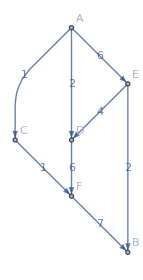

```mathematica
maxFlowGraph[op]
```

```mathematica
Subtract[x]
```

Subtract::argr: Subtract called with 1 argument; 2 arguments are expected.

Subtract[x]

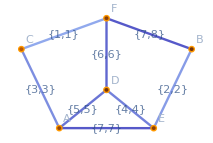

```mathematica
Graph[op["FlowGraph"],VertexLabels->"Name",EdgeLabels->((#->{op[#],PropertyValue[{op["FlowGraph"],#},EdgeCapacity]})&/@op["EdgeList"])]
```

```mathematica
FindMaximumFlow[]
```

```mathematica
NestWhile[NextKSubset[Range[Binomial[n+1,2]-1],#]&,Range[n-1],test]
```

```mathematica
NextKSubset[{1,2,3,4},{1,2}]
```

{1,3}

```mathematica
Clear[baseLine]
baseLine[n_Integer]:=NestList[NextKSubset[Range[Binomial[n+1,2]-1],#]&,Range[n-1],5]
```

```mathematica
baseLine[3]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4}}

```mathematica
Binomial[(n+1) n/2,n]n!/(Binomial[(n+1) n/2-1,n-1] n!)//FullSimplify
```

(1+n)/2

```mathematica
(DuplicateFreeQ@*Abs@*Differences)[{1,2,4,5,3,7,4}]
```

False

```mathematica
(Abs@*Differences)[{1,2,4,5,3,7,4}]
```

```mathematica
Equal[{1,2,1,2,4,3}]
```

True

```mathematica
Compile
```

```mathematica
Column@NestList[Abs@*Differences,#,Length[#]-1]&/@baseLine/@Range[5]
```

{{1},{1,3}
{2},{1,6,4}
{5,2}
{3},{6,1,10,8}
{5,9,2}
{4,7}
{3},{6,14,15,3,13}
{8,1,12,10}
{7,11,2}
{4,9}
{5}}

```mathematica
Differences[{1,2,3}]
```

{1,1}

```mathematica
solveTriangle[2]
```

{{Abs[x[2,1]-x[2,2]]==x[1,1],0<x[1,1]<3,0<x[2,1]<3,0<x[2,2]<3,x[1,1]≠x[2,1],x[1,1]≠x[2,2],x[2,1]≠x[2,2]},{x[1,1],x[2,1],x[2,2]},Integers}

```mathematica
solveTriangle2[n_Integer]:=Module[{vars=Flatten@Table[x[i,j],{i,n},{j,i}]},
Permutations]]
```

```mathematica
1/89.
```

0.011236

```mathematica
Module[{e1,e2},
e1=TransformedRegion[Disk[{-r,0},{1.8,1}],RotationTransform[60Degree,{-r,0}]];
e2=TransformedRegion[e1,RotationTransform[72 Degree]];
FindRoot[RegionDistance[e1,{x,y}]==0∧{x,y}∈e2,r]]
```

$Aborted

```mathematica
e1=TransformedRegion[Disk[{-2,0},{1.8,1}],RotationTransform[60Degree,{-2,0}]];
e2=TransformedRegion[e1,RotationTransform[72 Degree];
```

```mathematica
Table[Rotate[Rotate[Disk[{-2.5,0},{1.8,1}],70Degree],72k Degree,{0,0}],{k,0,1}]
```

```mathematica
GeometricTransformation[Disk[{0,0},{7/4,1}],RotationTransform[30Degree]]
```

Area::reg: GeometricTransformation[Disk[{0,0},{7/4,1}],{{{(√3)/2,-1/2},{1/2,(√3)/2}},{0,0}}] is not a correctly specified region.

```mathematica
Graphics@Table[Rotate[Rotate[Circle[{-2.5,0},{1.8,1}],70Degree],72k Degree,{0,0}],{k,0,4}]
```

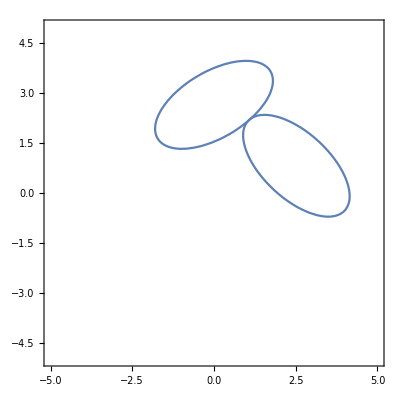

```mathematica
Show[ContourPlot[Evaluate[Total@((RotationMatrix[-θ].({x,y}+{0,-r})/{a,b})^2)==1/.{a->2,b->1,r->2.65,θ->30Degree}],{x,-5,5},{y,-5,5}],ContourPlot[Evaluate[Total@((RotationMatrix[-θ].(RotationMatrix[α].{x,y}+{0,-r})/{a,b})^2)==1/.{a->2,b->1,r->2.65,θ->30Degree,α->72Degree}],{x,-5,5},{y,-5,5}]]
```

```mathematica
NSolve[Total@((RotationMatrix[-θ].(RotationMatrix[α].{x,y}+{0,-r})/{a,b})^2)==1/.{a->2,b->1,r->2.65,θ->30Degree}/.{{α->0},{α->72Degree}},{x,y},Reals]
```

{{x→1.02556,y→2.14752},{x→1.14115,y→2.24727}}

$Aborted

```mathematica
Total@((RotationMatrix[-tilt].(RotationMatrix[θ].{x,y}+{0,-r})/{a,b})^2)==1/.{{θ->0},{θ->2π/n}}//Simplify
```

{((r-y) Cos[tilt]+x Sin[tilt])^2/b^2+(x Cos[tilt]+(-r+y) Sin[tilt])^2/a^2==1,(y Cos[(2 π)/n-tilt]-r Cos[tilt]+x Sin[(2 π)/n-tilt])^2/b^2+(-x Cos[(2 π)/n-tilt]+y Sin[(2 π)/n-tilt]+r Sin[tilt])^2/a^2==1}

```mathematica
ClearAll[eggsR]
eggsR[tilt_,r_,a_,b_:1,n_:5]:=RightComposition[Take[#,2]&,ReplaceAll[{x,y},#]&,Apply[SquaredEuclideanDistance],ReplaceAll[SquaredEuclideanDistance[x,y]->1]]@
NSolve[
{((r-y) Cos[tilt]+x Sin[tilt])^2/b^2+(x Cos[tilt]+(-r+y) Sin[tilt])^2/a^2==1,
(y Cos[(2 π)/n-tilt]-r Cos[tilt]+x Sin[(2 π)/n-tilt])^2/b^2+(-x Cos[(2 π)/n-tilt]+y Sin[(2 π)/n-tilt]+r Sin[tilt])^2/a^2==1},
{x,y},Reals]
```

Take::take: Cannot take positions 1 through 2 in {}.

ReplaceAll::reps: {Take[{},2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

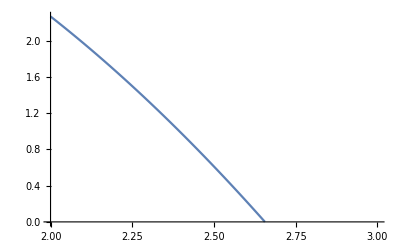

```mathematica
Plot[eggsR[30Degree,r,2],{r,2,3}]
```

```mathematica
{x,y}/.NSolve[
{((r-y) Cos[tilt]+x Sin[tilt])^2/b^2+(x Cos[tilt]+(-r+y) Sin[tilt])^2/a^2==1,
(y Cos[(2 π)/n-tilt]-r Cos[tilt]+x Sin[(2 π)/n-tilt])^2/b^2+(-x Cos[(2 π)/n-tilt]+y Sin[(2 π)/n-tilt]+r Sin[tilt])^2/a^2==1}/.{tilt->30Degree,a->2,b->1,n->5,r->3},
{x,y},Reals]
```

{x,y}

```mathematica
AppendTo[核算设计,(* 借方余额 = 1，贷方余额 = -1 *)
"科目信息"->Association@Query["表字段定义",
Select[StringMatchQ[#类型,"表*方"]&],
#变量名称-><|"科目方向"->2Boole@StringMatchQ[#类型,"*借方"]-1,"表"->#表|>&
]@核算设计];
```

```mathematica
AppendTo[核算设计,
"数据字典"->Normal@KeyMap[WordBoundary~~#~~WordBoundary&]@Join[Query["核算输入输出",All,"数据库表"]@核算设计,
Association@Query["表字段定义",All,(#变量名称->Query["核算输入输出",#表,"数据库表"][核算设计]<>"."<>#字段)&]@核算设计]];
```

```mathematica
AppendTo[核算设计,(* 不同业务下各科目的发生额 *)
"业务核算"->Map[KeyDrop["表外对拆"]]@Query[
"会计分录",
(e↦GroupBy[e,
Key["核算类型"]->(
<|#借方->核算设计["科目信息",#借方,"科目方向"]ToExpression[StringReplace[#金额,"."->"$"]],
#贷方->-核算设计["科目信息",#贷方,"科目方向"]ToExpression[StringReplace[#金额,"."->"$"]]|>&),
Merge[Total/*InputForm/*ToString]])
]@核算设计];
```

```mathematica
AppendTo[核算设计,
"会计分录文本"->Query["核算设计文本",
Association@StringCases[
StringExpression[
StartOfLine~~"#+NAME: acc:会计分录"~~Whitespace,
tcnt:Shortest["|-"~~__~~"-|\n"],
"\n"]:>(StringTrim@First@StringSplit[StringSplit[tcnt,"\n"][[4]],"|"]->tcnt)]
]@核算设计];
```

```mathematica
Clear[映射字段, 存储过程]

映射字段[中文字段_List]:=StringRiffle[StringReplace[中文字段,核算设计["数据字典"]],", "]

存储过程[业务类型_String]:=Module[{持仓核算字段,资金核算字段},
{持仓核算字段,资金核算字段}=Map[t↦Query["业务核算",业务类型,KeySelect[核算设计["科目信息",#,"表"]==t&]]@核算设计]@{"持仓核算","资金核算"};
TemplateApply[核算设计["存储过程模板"],
Join[
Query["核算输入输出",All,"数据库表"]@核算设计,
Query["核算办法",业务类型]@核算设计,
<|
"会计分录"->核算设计["会计分录文本",业务类型],
"业务类型" -> 业务类型, 
"流通类型" ->"'"<>StringTake["0"<>核算设计["核算办法",业务类型,"流通类型"],-2]<>"'",
"持仓核算字段"->", "<>映射字段[Keys@持仓核算字段],
"持仓核算发生额"->", "<>映射字段[Values@持仓核算字段],
"资金核算字段"->", "<>映射字段[Keys@资金核算字段],
"资金核算发生额"->", "<>映射字段[Values@资金核算字段],
"持仓核算更新"->映射字段[KeyValueMap[#1<>" = "<>#2&,持仓核算字段]],
"资金核算更新"->映射字段[KeyValueMap[#1<>" = "<>#2&,资金核算字段]]
|>]]]
```

```mathematica
Export["test.sql",TemplateApply[Import["tpl_merge.sql","Text",CharacterEncoding->"UTF8"], <|"业务流水表"->"logasset_hs","持仓核算表"->"stkasset_hs", "业务类型" -> "红利入账", "业务摘要" -> "221007","会计分录"->核算设计["会计分录文本","红利入账"]|>],"Text",CharacterEncoding->"UTF8"]
```

```mathematica
Nest[t↦TemplateApply[t,<|"业务流水表"->"logasset_hs","持仓核算表"->"stkasset_hs", "业务类型" -> "红利入账", "业务摘要" -> "221007","会计分录"->核算设计["会计分录文本","红利入账"]|>],Import["tpl_merge.sql","Text",CharacterEncoding->"UTF8"],2]
```

```mathematica
Intersection[Keys@核算设计["业务核算","红利入账"],Query["表字段定义",Select[#表=="资金核算"&&StringMatchQ[#类型,"表*方"]&]/*Keys]@核算设计]
```

{账户资金}

```mathematica
核算设计["业务核算","红利入账"]
```

<|账户资金→成交金额,利息收入→成交金额,表外对拆→成交金额,红利金额→成交金额|>

```mathematica
TemplateApply[核算设计["存储过程模板","会计核算"],
<|"业务流水表"->"logasset_hs",
"持仓核算表"->"stkasset_hs", 
"业务类型" -> "红利入账", 
"业务摘要" -> "221007",
"会计分录"->核算设计["会计分录文本","红利入账"]|>]
```

/***************************************************
    业务类型:	红利入账
    业务摘要:	221007


    本存储过程由以下会计分录自动生成：

|----------+----------+----------+----------+--------------|
| 业务类型 | 借方     | 贷方     | 金额     | 说明         |
|----------+----------+----------+----------+--------------|
| 红利入账 | 账户资金 | 利息收入 | 成交金额 | 利息收入入账 |
|----------+----------+----------+----------+--------------|
| 红利入账 | 表外对拆 | 红利金额 | 成交金额 | 红利金额记录 |
|----------+----------+----------+----------+--------------|


*/

if exists (select * from sysobjects where type = 'P' and name = 'sp_221007')
	drop procedure sp_221007
go

create procedure sp_221007(
	@bizdate int,  
	@msg varchar(128) = null output)
as
begin try
	begin transaction

		-- 更新持仓核算表
	merge into  as sec
	using (
		select serverid, orgid, custid, fundid, market, stkcode,  as ltlx
		from 
		where digestid =  and bizdate = @bizdate
	) as ord
	on (
		sec.serverid = ord.serverid and
		sec.orgid = ord.orgid and
		sec.custid = ord.custid and
		sec.fundid = ord.fundid and
		sec.market = ord.market and
		sec.ltlx = ord.ltlx and
		sec.stkcode = ord.stkcode)
	when matched then
		update set 
	when not matched then
		insert (serverid, orgid, custid, fundid, market, stkcode, ltlx)  
		values (ord.serverid, ord.orgid, ord.custid, ord.fundid, ord.market, ord.stkcode, ord.ltlx);

	

	select @msg='核算处理成功'

	update logasset_hs set sett_status = 3, sett_remark = @msg
	where  bizdate = @bizdate and digestid = 221007 and bizdate = @bizdate

	commit transaction
	return 0
end try

begin catch
	if @@trancount > 0
		rollback transaction
	
	return -1
end catch

go

```mathematica
StringReplace[Keys@First@KeyIntersection[{核算设计["业务核算","红利入账"],
Query["表字段定义",Select[#表=="持仓核算"&]]@核算设计}]]
```

{"利息收入", "红利金额"}

```mathematica
translateDB[biz_String->params_]:=biz->Map[Lookup[科目增减[biz],#,#]&,params]
```

```mathematica
Query["公共过程参数",All,"赋值"]@核算设计
```

<|@action→,@matchqty→成交数量,@matchamt→成交金额,@matchamt_ex→0,@aiamount→0,@fundeffect→账户资金,@stkeffect→库存数量,@stkcost_ch→库存成本,@syvalue_ch→交易收益,@aicost_ch→利息成本,@lxsr_ch→利息收入,@fee→总费用,@jsxf→净手续费,@yhs→印花税,@ghf→过户费,@qtfee→其它费,@lxs→利息税|>